```mathematica
If[#==1,1,With[{l=Rest@Reverse@Divisors@#},Min[#0/@l+#/l+2]]]&[10000]
```

所有临时定义已清空!

1 | 
2 | ACVV
3 | ACVVV
4 | ACVVVV
5 | ACVVVVV
6 | ACVVVVVV
7 | ACVVVVVVV
8 | ACVVVVACVV
9 | ACVVVACVVV
10 | ACVVVVVACVV
11 | ACVVVVVVVVVVV
12 | ACVVVVACVVV
13 | ACVVVVVVVVVVVVV
14 | ACVVVVVVVACVV
15 | ACVVVVVACVVV
16 | ACVVVVACVVVV
17 | ACVVVVVVVVVVVVVVVVV
18 | ACVVVVVVACVVV
19 | ACVVVVVVVVVVVVVVVVVVV
20 | ACVVVVVACVVVV

14.8977

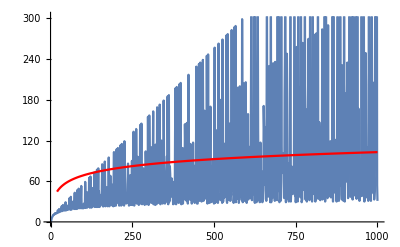

```mathematica
CC
stdp[1]=ConstantArray["V",dp[1]=0];
dp[i_]:=dp[i]=With[{l=Rest@Reverse@Divisors[i]},Min[dp/@l+i/l+2]];
stdp[i_]:=stdp[i]=Block[
{l=Rest@Reverse@Divisors[i],st},
st=Take[l,Ordering[dp/@l+i/l+2,1]];
Join[stdp@@st,{"A","C"},ConstantArray["V",i/First@st]]
]
TableForm[StringJoin@@@Array[stdp,20],TableHeadings->{Range[20],None}]
α=a/.FindFit[data={#,dp@#}&/@DeleteCases[Range[1000],_?PrimeQ],a Log[x],a,x]
Show[ListLinePlot@data,Plot[a Log[x]/.{a->α},{x,1,1000},PlotStyle->Red]]
```

```mathematica
StringLength/@StringJoin@@@Array[stdp,20]
Array[dp,20]
```

{0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13}

{0,4,5,6,7,8,9,10,10,11,13,11,15,13,12,12,19,13,21,13}

所有临时定义已清空!

1 | P
2 | PP
3 | PPP
4 | PPPP
5 | PPPPP
6 | PPPPPP
7 | PPPPPPP
8 | PPPPACVV
9 | PPPACVVV
10 | PPPPPACVV
11 | PPPPPACVVP
12 | PPPPACVVV
13 | PPPPACVVVP
14 | PPPPPPPACVV
15 | PPPPPACVVV
16 | PPPPACVVVV
17 | PPPPACVVVVP
18 | PPPPPPACVVV
19 | PPPPPPACVVVP
20 | PPPPPACVVVV

4.35639

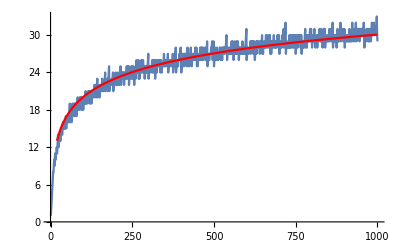

```mathematica
CC
stdp[1]=ConstantArray["P",dp[1]=1];
dp[i_]:=dp[i]=With[
{l=Rest@Reverse@Divisors[i]},
Min@Append[dp/@l+i/l+2,dp[i-1]+1]
];
stdp[i_]:=stdp[i]=Block[
{l=Rest@Reverse@Divisors[i],st},
st=Ordering[Join[dp/@l+i/l+2,{dp[i-1]+1}],1];
If[First@st>Length[l],
Append[stdp[i-1],"P"],
Join[stdp@@Take[l,st],{"A","C"},ConstantArray["V",i/First@Take[l,st]]]
]
]
TableForm[StringJoin@@@Array[stdp,20],TableHeadings->{Range[20],None}]
α=a/.FindFit[data=Array[dp,1000],a Log[x],a,x]
Show[ListLinePlot@data,Plot[a Log[x]/.{a->α},{x,1,1000},PlotStyle->Red]]
```

```mathematica
3^(4-n+5 Floor[n/5]) 4^(n-3-4 Floor[n/5])/.n->100

LinearRecurrence[
{0,0,0,0,4},
{1,2,3,4,5,6,9,12,16,20,27,36,48,64,81},
{100}
]//First

nt=x (1+2 x+3 x^2+4 x^3+5 x^4+2 x^5+x^6+3 x^10+x^14);
SeriesCoefficient[Series[nt/(1-4*x^5),{x,0,100}],100]
```

1391569403904

1391569403904

1391569403904

所有临时定义已清空!

-Graphics-

4.10679

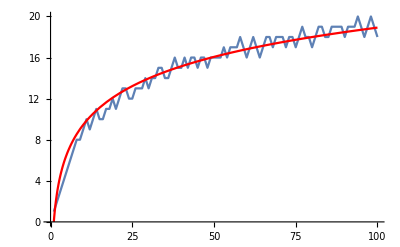

```mathematica
CC
n=100;
cost[i_]:=Block[
{P=1,D=1,S=2,V=1,l},
l=Drop[Divisors[i],-1];
Join[
Transpose[{Thread[l->i],S+i/l V}],
{{i-1->i,P},{i+1->i,D}}
]
]
raw=Drop[Flatten[Table[cost[i],{i,1,n+10}],1],-1];
{dir,wei}=Transpose[(SortBy[#,Last]&/@GatherBy[raw,First])[[All,1]]];
G=Graph[dir,EdgeWeight->wei,PlotTheme->"Monochrome",GraphLayout->"CircularEmbedding"]
ways=FindShortestPath[G,0,All]/@Range[n];
dis=GraphDistance[G,0,#]&/@Range[n]//Round;
α=a/.FindFit[dis,a Log[x],a,x]
Show[ListLinePlot@dis,Plot[a Log[x]/.{a->α},{x,1,n},PlotStyle->Red]]
```

```mathematica
SortBy[ways,Length]
dis
```

{{0,1},{0,1,2},{0,1,2,3},{0,1,2,8},{0,1,2,10},{0,1,2,14},{0,1,2,3,4},{0,1,2,3,9},{0,1,2,3,12},{0,1,2,3,15},{0,1,2,3,18},{0,1,2,3,21},{0,1,2,10,11},{0,1,2,10,50},{0,1,2,10,70},{0,1,2,14,98},{0,1,2,3,4,5},{0,1,2,3,4,16},{0,1,2,3,4,20},{0,1,2,3,4,24},{0,1,2,3,4,28},{0,1,2,3,4,32},{0,1,2,3,9,27},{0,1,2,3,9,45},{0,1,2,3,9,54},{0,1,2,3,9,63},{0,1,2,3,12,13},{0,1,2,3,12,48},{0,1,2,3,12,60},{0,1,2,3,12,72},{0,1,2,3,12,84},{0,1,2,3,15,75},{0,1,2,3,15,90},{0,1,2,3,21,22},{0,1,2,10,11,33},{0,1,2,10,11,44},{0,1,2,10,11,55},{0,1,2,10,11,66},{0,1,2,10,11,77},{0,1,2,3,4,5,6},{0,1,2,3,4,5,25},{0,1,2,3,4,5,30},{0,1,2,3,4,5,35},{0,1,2,3,4,5,40},{0,1,2,3,4,16,17},{0,1,2,3,4,16,64},{0,1,2,3,4,16,80},{0,1,2,3,4,16,96},{0,1,2,3,4,20,19},{0,1,2,3,4,20,100},{0,1,2,3,4,24,23},{0,1,2,3,4,28,29},{0,1,2,3,9,27,81},{0,1,2,3,9,45,46},{0,1,2,3,12,13,39},{0,1,2,3,12,13,52},{0,1,2,3,12,13,65},{0,1,2,3,12,13,78},{0,1,2,3,12,13,91},{0,1,2,3,12,48,47},{0,1,2,3,12,60,59},{0,1,2,3,12,60,61},{0,1,2,3,12,72,71},{0,1,2,3,12,72,73},{0,1,2,3,12,84,83},{0,1,2,3,15,75,74},{0,1,2,3,15,90,89},{0,1,2,3,21,22,88},{0,1,2,3,4,5,6,7},{0,1,2,3,4,5,6,36},{0,1,2,3,4,5,6,42},{0,1,2,3,4,5,25,26},{0,1,2,3,4,5,30,31},{0,1,2,3,4,5,40,41},{0,1,2,3,4,16,17,34},{0,1,2,3,4,16,17,51},{0,1,2,3,4,16,17,68},{0,1,2,3,4,16,17,85},{0,1,2,3,4,16,80,79},{0,1,2,3,4,16,96,97},{0,1,2,3,4,20,19,38},{0,1,2,3,4,20,19,57},{0,1,2,3,4,20,19,76},{0,1,2,3,4,20,19,95},{0,1,2,3,4,20,100,99},{0,1,2,3,4,24,23,69},{0,1,2,3,4,24,23,92},{0,1,2,3,4,28,29,58},{0,1,2,3,4,28,29,87},{0,1,2,3,9,27,81,82},{0,1,2,3,12,13,52,53},{0,1,2,3,12,48,47,94},{0,1,2,3,4,5,6,7,49},{0,1,2,3,4,5,6,7,56},{0,1,2,3,4,5,6,36,37},{0,1,2,3,4,5,6,42,43},{0,1,2,3,4,5,30,31,62},{0,1,2,3,4,5,30,31,93},{0,1,2,3,4,16,17,68,67},{0,1,2,3,4,16,17,85,86}}

{1,2,3,4,5,6,7,8,8,9,10,9,10,11,10,10,11,11,12,11,12,13,13,12,12,13,13,13,14,13,14,14,15,15,14,14,15,16,15,15,16,15,16,16,15,16,16,15,16,16,16,16,17,16,17,17,17,18,17,16,17,18,17,16,17,18,18,17,18,18,18,17,18,18,17,18,19,18,18,17,18,19,19,18,18,19,19,19,19,18,19,19,19,20,19,18,19,20,19,18}

```mathematica
TravelingSalesman
```

```mathematica
KochCurve
```

```mathematica
切比雪夫
```

```mathematica
raw
```

{{0→1,1},{2→1,1},{1→2,4},{1→2,1},{3→2,1},{1→3,5},{2→3,1},{4→3,1},{1→4,6},{2→4,4},{3→4,1},{5→4,1},{1→5,7},{4→5,1},{6→5,1},{1→6,8},{2→6,5},{3→6,4},{5→6,1},{7→6,1},{1→7,9},{6→7,1},{8→7,1},{1→8,10},{2→8,6},{4→8,4},{7→8,1},8107,{42→1008,26},{48→1008,23},{56→1008,20},{63→1008,18},{72→1008,16},{84→1008,14},{112→1008,11},{126→1008,10},{144→1008,9},{168→1008,8},{252→1008,6},{336→1008,5},{504→1008,4},{1007→1008,1},{1009→1008,1},{1→1009,1011},{1008→1009,1},{1010→1009,1},{1→1010,1012},{2→1010,507},{5→1010,204},{10→1010,103},{101→1010,12},{202→1010,7},{505→1010,4},{1009→1010,1}}
 |  |  |  |

```mathematica
CC
dl[0]=dp[0]=0;
dp[1]=1;
dp[i_]:=dp[i]=With[
{l=Rest@Reverse@Divisors[i]},
Min@Append[dp/@l+i/l+2,dp[i-1]+1]
];
dl[i_]:=Min[dp[i],dp[i-1]]
Array[dl,100]
```

所有临时定义已清空!

```mathematica
{0,1,2,3,4,5,6,7,8,8,9,9,9,10,10,10,10,11,11,11,11,12,13,12,12,12,13,13,13,13,13,14,14,15,14,14,14,15,15,15,15,15,15,16,15,15,16,15,15,16,16,16,16,16,16,17,17,17,18,16,16,17,17,16,16,17,18,17,17,18,18,17,17,18,17,17,18,18,18,17,17,18,19,18,18,18,19,19,19,18,18,19,19,19,19,18,18,19,20,18}-{1,2,3,4,5,6,7,8,8,9,10,9,10,11,10,10,11,11,12,11,12,13,13,12,12,13,13,13,14,13,14,14,15,15,14,14,15,16,15,15,16,15,16,16,15,16,16,15,16,16,16,16,17,16,17,17,17,18,17,16,17,18,17,16,17,18,18,17,18,18,18,17,18,18,17,18,19,18,18,17,18,19,19,18,18,19,19,19,19,18,19,19,19,20,19,18,19,20,19,18}
```

{-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,0,-1,-1,0,0,-1,0,-1,0,-1,-1,0,0,0,-1,0,0,-1,0,-1,0,-1,0,0,0,-1,-1,0,0,-1,0,-1,0,0,-1,0,0,-1,0,0,0,-1,0,-1,0,0,-1,1,0,-1,-1,0,0,-1,-1,0,0,-1,0,0,0,-1,0,0,-1,-1,0,0,0,-1,-1,0,0,0,-1,0,0,0,0,-1,0,0,-1,0,0,-1,-1,1,0}

```mathematica
dp[i_]:=dp[i]=If[i==1,1,With[{l=Rest@Reverse@Divisors[i]},Min[dp/@l+i/l+2]]];
dp[10]
```

12

```mathematica
If[#1==1,1,With[{l=Rest@Reverse@Divisors@#1},Min[#0/@l+#1/l+2]]]&[10]
```

12

41

```mathematica
CC
```

所有临时定义已清空!

```mathematica
trans[a_,b_]:=Join[
Table[{st[a,b]->st[a,j],2},{j,b+1,a}],
{{st[a,b]->st[a+b,b],1},{st[a,b]->st[a+1,b],1}}
];
trans[a_,0]:=Append[Table[{st[a,0]->st[a,j],2},{j,1,a}],{st[a,0]->st[a+1,0],1}];
trans[n_]:=Flatten[Table[trans[n,i],{i,0,n}],1];
GetPath[G_,n_]:=Block[{list,min,path},
list=Table[GraphDistance[G,st[0,0],st[n,i]],{i,0,n}];
min=Round@Flatten@Position[list,Min@list];
path=Table[FindShortestPath[G,st[0,0],All][st[10,i]],{i,min}];
Association["Min"->Round@Min@list,"Path"->First@path]
];
```

```mathematica
(n=100;
raw=DeleteCases[
Flatten[Array[trans,n],1]~Append~{st[0,0]->st[1,0],1},
#[[1,2,1]]>n||#[[1,2]]==#[[1,1]]&
];
{dir,wei}=Transpose[(SortBy[#,Last]&/@GatherBy[raw,First])[[All,1]]];
G=Graph[dir,EdgeWeight->wei,GraphLayout->"LargeGraph"]
)//TTT
```

CPU Time:  1.39063 s

Memory used:  23.9666 MB

All Time:  1.629222

```mathematica
GetPath[G,50]//TTT
```

CPU Time:  0.671875 s

Memory used:  0.264104 MB

<|Min→14,Path→ShortestPathFunction[{st[0,0],All},«»][st[10,11]]|>

All Time:  48.7166391

<|Min→10,Path→{st[0,0],st[1,0],st[2,0],st[3,0],st[4,0],st[5,0],st[5,5],st[10,5]}|>

```mathematica
step[n_]:=Min@Table[GraphDistance[G,st[0,0],st[n,i]],{i,0,n}]//Round
data=step/@Range[100]//TTT
```

CPU Time:  62.2344 s

Memory used:  0.003984 MB

{1,2,3,4,5,6,7,7,7,8,9,8,9,10,9,9,10,10,11,10,11,11,11,11,11,12,11,12,12,12,12,12,12,12,13,12,13,13,13,13,13,13,13,13,13,13,14,13,14,14,14,14,14,14,14,14,14,14,15,14,14,15,15,14,15,15,15,15,15,15,15,15,15,15,15,15,15,16,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

All Time:  85.1466448